## Prelim

### Creating some functions for linear transformations

```mathematica
A[r_]:={{0,-r[[3]],r[[2]]},{r[[3]],0,-r[[1]]},{-r[[2]],r[[1]],0}};
```

```mathematica
Q[rvec_,θ_]:=(1-Cos[θ])*rvec⊗rvec+Cos[θ]*IdentityMatrix[3]+Sin[θ]*A[rvec];
```

```mathematica
T[u_,c_]:=u+c;
```

```mathematica
RotateAbout[QMat_,c_,x_]:=T[QMat.T[x,-c],c];
```

```mathematica
MatrixProduct[As_]:=Module[{ret,i},
ret=IdentityMatrix[Length[As[[1]]]];
For[i=1,i≤Length[As],i++,
ret=ret.As[[i]];
];
ret
]
```

```mathematica
QRod[ω_]:=Module[{r,θ},
θ=Norm[ω];
r=If[θ>0,ω/θ,ω];
Return[If[θ>0,Q[r,θ],IdentityMatrix[3]]];
]
```

#### Worm-like chain free energy

```mathematica
Wwlc[λ_]:=kT*k*(2*λ^2+1/(1-λ)-λ)
```

```mathematica
D[Wwlc[Sqrt[x]],{x,2}]
```

k kT (1/(4 x^(3/2))-1/(4 (1-√x)^2 x^(3/2))+1/(2 (1-√x)^3 x))

```mathematica
d2Wwlcdx2=Simplify[D[Wwlc[Sqrt[x]],{x,2}]]
```

(k kT (-3+√x))/(4 (-1+√x)^3 √x)

Clearly, this is convex with respect to x^2

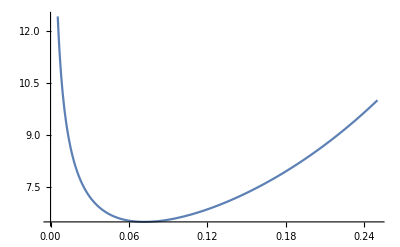

```mathematica
Plot[d2Wwlcdx2/.{k*kT->1},{x,0,0.25}]
```

Thus, Wormlike chain also should satisfy the equipartition property (i.e. it is a convex function of the stretch squared)

### Freely jointed chain (KG approximation)

```mathematica
LangInv[x_]:=3*x+x^2/5*Sin[7*x/2]+x^3/(1-x)
```

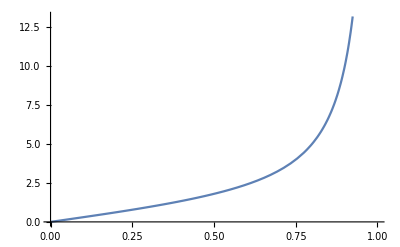

```mathematica
Plot[LangInv[x],{x,0,1}]
```

```mathematica
WLang[γ_]:=Module[{β},
β=LangInv[γ];
Return[γ*β+Log[β*Csch[β]]];
]
```

## Unification of discrete polymer network models

```mathematica
$Assumptions=θ∈Reals&&ϕ∈Reals&&ψ∈Reals
```

θ∈ℝ&&ϕ∈ℝ&&ψ∈ℝ

Reference end-to-end vectors for the 4-chain model

```mathematica
c4Rs=r0*{{0,0,1},{0,2*Sqrt[2]/3,-1/3},{Sqrt[2/3],-Sqrt[2]/3,-1/3},{-Sqrt[2/3],-Sqrt[2]/3,-1/3}}
```

{{0,0,r0},{0,(2 √2 r0)/3,-r0/3},{√(2/3) r0,-(√2 r0)/3,-r0/3},{-√(2/3) r0,-(√2 r0)/3,-r0/3}}

This is a generic symmetric 3x3 matrix

```mathematica
testC={{c[1,1],c[1,2],c[1,3]},{c[1,2],c[2,2],c[2,3]},{c[1,3],c[2,3],c[3,3]}};
```

This shows that the sum of the square stretch is conserved

```mathematica
Simplify[Sum[c4Rs[[j]].testC.c4Rs[[j]],{j,1,4}]]
```

4/3 r0^2 (c[1,1]+c[2,2]+c[3,3])

Reference end-to-end vectors for the 8-chain model; sum of the square stretch is conserved

```mathematica
c8Rs=r0/(√3)*ArrayReshape[Table[{(-1)^(i-1),(-1)^(j-1),(-1)^(k-1)},{i,1,2},{j,1,2},{k,1,2}],{8,3}]
```

{{r0/(√3),r0/(√3),r0/(√3)},{r0/(√3),r0/(√3),-r0/(√3)},{r0/(√3),-r0/(√3),r0/(√3)},{r0/(√3),-r0/(√3),-r0/(√3)},{-r0/(√3),r0/(√3),r0/(√3)},{-r0/(√3),r0/(√3),-r0/(√3)},{-r0/(√3),-r0/(√3),r0/(√3)},{-r0/(√3),-r0/(√3),-r0/(√3)}}

```mathematica
Simplify[Sum[c8Rs[[j]].testC.c8Rs[[j]],{j,1,8}]]
```

8/3 r0^2 (c[1,1]+c[2,2]+c[3,3])

Reference end-to-end vectors for the 3-chain model; sum of the square stretch is conserved

```mathematica
c3Rs=r0*{{1,0,0},{0,1,0},{0,0,1}}
```

{{r0,0,0},{0,r0,0},{0,0,r0}}

```mathematica
Simplify[Sum[c3Rs[[j]].testC.c3Rs[[j]],{j,1,3}]]
```

r0^2 (c[1,1]+c[2,2]+c[3,3])

```mathematica
r0sub={r0->b*√n};
ω0=1/(√3){π/4,π/4,π/4}
```

{π/(4 √3),π/(4 √3),π/(4 √3)}

```mathematica
New3Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c3Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,3}]/3,{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New3ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c3Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,3}]/3,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
```

```mathematica
New8Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c8Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,8}]/8,{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New8ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c8Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,8}]/8,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
Standard8Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{λ},
λ=Sqrt[Tr[Transpose[F].F]/(3*nv)];
f[λ]
]
```

```mathematica
New4Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c4Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,4}],{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New4ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c4Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,4}]/4,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
```

```mathematica
uniF[λ_]:={{λ,0,0},{0,1/Sqrt[λ],0},{0,0,1/Sqrt[λ]}}
```

```mathematica
New4ChainLocal[uniF[1]]
```

{0.0150453,{ωx→0.45345,ωy→0.45345,ωz→0.45345}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

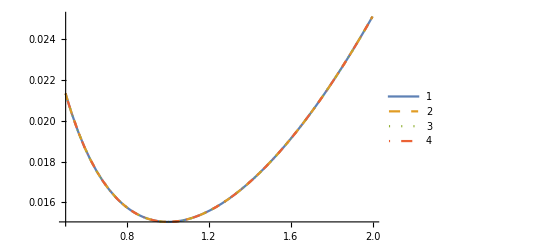

```mathematica
Plot[{New3ChainLocal[uniF[λ]][[1]],New4ChainLocal[uniF[λ]][[1]],New8ChainLocal[uniF[λ]][[1]],Standard8Chain[uniF[λ]]},{λ,0.5,2.0},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dotted,DotDashed},MaxRecursion->5]
```

```mathematica
shearF[s_]:={{1,0,s},{0,1,0},{0,0,1}}
```

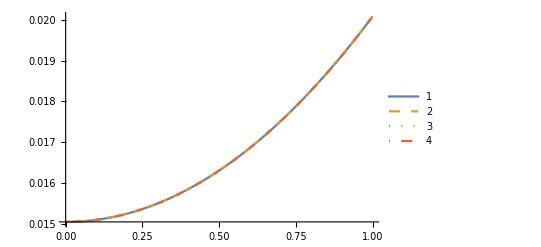

```mathematica
Plot[{New3ChainLocal[shearF[λ]][[1]],New4ChainLocal[shearF[λ]][[1]],New8ChainLocal[shearF[λ]][[1]],Standard8Chain[shearF[λ]]},{λ,0.0,1.0},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dotted,DotDashed},MaxRecursion->5]
```

Let’s compare the new 8 chain to the standard Arruda-Boyce

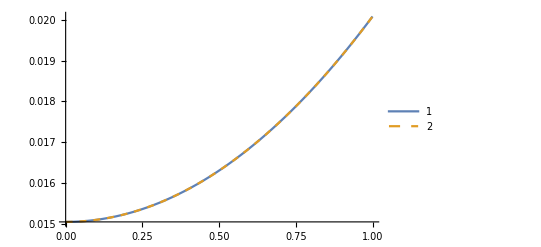

```mathematica
Plot[{New8ChainLocal[shearF[λ]][[1]],Standard8Chain[shearF[λ]]},{λ,0.0,1.0},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dotted},MaxRecursion->5]
```

### Find conditions on similarity transformation of C for the equipartition of stretch for 4-chain model

```mathematica
CTest2={{Ce[1,1],Ce[1,2],Ce[1,3]},{Ce[1,2],Ce[2,2],Ce[2,3]},{Ce[1,3],Ce[2,3],Ce[3,3]}};
```

```mathematica
λTest2=Simplify[Table[c4Rs[[i]].(CTest2.c4Rs[[i]])/(r0^2),{i,1,4}]]
```

{Ce[3,3],1/9 (8 Ce[2,2]-4 √2 Ce[2,3]+Ce[3,3]),1/9 (6 Ce[1,1]-4 √3 Ce[1,2]-2 √6 Ce[1,3]+2 Ce[2,2]+2 √2 Ce[2,3]+Ce[3,3]),1/9 (6 Ce[1,1]+4 √3 Ce[1,2]+2 √6 Ce[1,3]+2 Ce[2,2]+2 √2 Ce[2,3]+Ce[3,3])}

```mathematica
sub=Solve[3*Ce[3,3]==Simplify[λTest2[[3]]+λTest2[[4]]+λTest2[[2]]],Ce[3,3]]
```

{{Ce[3,3]→1/2 (Ce[1,1]+Ce[2,2])}}

```mathematica
λTest3=Simplify[λTest2/.sub[[1]]]
```

{1/2 (Ce[1,1]+Ce[2,2]),1/18 (Ce[1,1]+17 Ce[2,2]-8 √2 Ce[2,3]),1/18 (13 Ce[1,1]-8 √3 Ce[1,2]-4 √6 Ce[1,3]+5 Ce[2,2]+4 √2 Ce[2,3]),1/18 (13 Ce[1,1]+8 √3 Ce[1,2]+4 √6 Ce[1,3]+5 Ce[2,2]+4 √2 Ce[2,3])}

```mathematica
sub2=Solve[λTest3[[1]]==λTest3[[2]],Ce[2,3]]
```

{{Ce[2,3]→-(Ce[1,1]-Ce[2,2])/(√2)}}

```mathematica
λTest4=Simplify[λTest3/.sub2[[1]]]
```

{1/2 (Ce[1,1]+Ce[2,2]),1/2 (Ce[1,1]+Ce[2,2]),1/18 (9 Ce[1,1]-8 √3 Ce[1,2]-4 √6 Ce[1,3]+9 Ce[2,2]),1/18 (9 Ce[1,1]+8 √3 Ce[1,2]+4 √6 Ce[1,3]+9 Ce[2,2])}

```mathematica
sub3=Simplify[Solve[-8 √3 Ce[1,2]-4 √6 Ce[1,3]==0,{Ce[1,2]}]]
```

{{Ce[1,2]→-Ce[1,3]/(√2)}}

```mathematica
λTest5=Simplify[λTest4/.sub3[[1]]]
```

{1/2 (Ce[1,1]+Ce[2,2]),1/2 (Ce[1,1]+Ce[2,2]),1/2 (Ce[1,1]+Ce[2,2]),1/2 (Ce[1,1]+Ce[2,2])}

Test conditions numerically...

```mathematica
Manipulate[Block[{result4,F,C,CPrime,rs,ω,Qt,λs,ω0,Rs},
F=uniF[λ];
C=Transpose[F].F;
result4=Quiet[New4ChainLocal[uniF[λ],WLang,100,1]];
ω={ωx,ωy,ωz}/.result4[[2]];
Qt=QRod[ω];
Rs=c4Rs/.{r0->b*√n};
rs=Table[uniF[λ].QRod[ω].Rs[[i]],{i,1,4}]/.{n->100,b->1};
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,4}];
CPrime=Transpose[Qt].C.Qt;
{"F=",MatrixForm[F],"F'=",MatrixForm[Transpose[Qt].F.Qt],"C=",MatrixForm[C],"C'=",MatrixForm[CPrime],"1/3 Tr[C]=",Tr[C]/3,"C'[3,3]=",CPrime[[3]][[3]],"-(C'[1, 1] - C'[2, 2])/(√2)=",-(CPrime[[1]][[1]]-CPrime[[2]][[2]])/(√2),"C'[2,3]=",CPrime[[2]][[3]],"Eigensystem[C]=",Eigensystem[C],"Q=",MatrixForm[Qt],"rs=",MatrixForm[rs],"λs=",MatrixForm[λs],"√((C'[1, 1] + C'[2, 2])/(2 SuperscriptBox[n, 2] b))=",√((CPrime[[1]][[1]]+CPrime[[2]][[2]])/(2*100*1^2)),"√((Tr C')/(2 SuperscriptBox[n, 2] b))=",√(Tr[CPrime]/(3*100*1^2))}
],{{λ,1.0},0.1,10.0,0.1}]
```

```mathematica
Manipulate[Block[{result4,F,C,CPrime,rs,ω,Qt,λs,ω0,Rs},
F=shearF[s];
C=Transpose[F].F;
result4=Quiet[New4ChainLocal[F,WLang,100,1]];
ω={ωx,ωy,ωz}/.result4[[2]];
Qt=QRod[ω];
Rs=c4Rs/.{r0->b*√n};
rs=Table[F.QRod[ω].Rs[[i]],{i,1,4}]/.{n->100,b->1};
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,4}];
CPrime=Transpose[Qt].C.Qt;
{"F=",MatrixForm[F],"F'=",MatrixForm[Transpose[Qt].F.Qt],"C=",MatrixForm[C],"C'=",MatrixForm[CPrime],"1/3 Tr[C]=",Tr[C]/3,"C'[3,3]=",CPrime[[3]][[3]],"-(C'[1, 1] - C'[2, 2])/(√2)=",-(CPrime[[1]][[1]]-CPrime[[2]][[2]])/(√2),"C'[2,3]=",CPrime[[2]][[3]],"Eigensystem[C]=",Eigensystem[C],"Q=",MatrixForm[Qt],"rs=",MatrixForm[rs],"λs=",MatrixForm[λs],"√((C'[1, 1] + C'[2, 2])/(2 SuperscriptBox[n, 2] b))=",√((CPrime[[1]][[1]]+CPrime[[2]][[2]])/(2*100*1^2)),"√((Tr C')/(2 SuperscriptBox[n, 2] b))=",√(Tr[CPrime]/(3*100*1^2))}
],{{s,1.0},0.1,10.0,0.1}]
```

```mathematica
Manipulate[Block[{result4,F,C,CPrime,rs,ω,Qt,λs,ω0,Rs},
F={{λ1,0,0},{0,λ2,0},{0,0,λ3}};
C=Transpose[F].F;
result4=Quiet[New4ChainLocal[F,WLang,100,1]];
ω={ωx,ωy,ωz}/.result4[[2]];
Qt=QRod[ω];
Rs=c4Rs/.{r0->b*√n};
rs=Table[F.QRod[ω].Rs[[i]],{i,1,4}]/.{n->100,b->1};
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,4}];
CPrime=Transpose[Qt].C.Qt;
{"F=",MatrixForm[F],"F'=",MatrixForm[Transpose[Qt].F.Qt],"C=",MatrixForm[C],"C'=",MatrixForm[CPrime],"1/3 Tr[C]=",Tr[C]/3,"C'[3,3]=",CPrime[[3]][[3]],"-(C'[1, 1] - C'[2, 2])/(√2)=",-(CPrime[[1]][[1]]-CPrime[[2]][[2]])/(√2),"C'[2,3]=",CPrime[[2]][[3]],"Eigensystem[C]=",Eigensystem[C],"Q=",MatrixForm[Qt],"rs=",MatrixForm[rs],"λs=",MatrixForm[λs],"√((C'[1, 1] + C'[2, 2])/(2 SuperscriptBox[n, 2] b))=",√((CPrime[[1]][[1]]+CPrime[[2]][[2]])/(2*100*1^2)),"√((Tr C')/(2 SuperscriptBox[n, 2] b))=",√(Tr[CPrime]/(3*100*1^2))}
],{{λ1,1.0},0.1,10.0,0.1},{{λ2,1.0},0.1,10.0,0.1},{{λ3,1.0},0.1,10.0,0.1}]
```

### Proof for 4-chain

```mathematica
Clear[λ1,λ2,λ3]
```

```mathematica
Cdiag={{λ1^2,0,0},{0,λ2^2,0},{0,0,λ3^2}};
```

```mathematica
MatrixForm[QGen=Q[{1,0,0},α].Q[{0,1,0},β].Q[{0,0,1},γ]]
```

(Cos[β] Cos[γ] | -Cos[β] Sin[γ] | Sin[β]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

```mathematica
Rrels=c4Rs/r0;
```

```mathematica
MatrixForm[λ2rels=Simplify[Table[(QGen.Rrels[[i]]).Cdiag.(QGen.Rrels[[i]]),{i,1,4}]]]
```

(λ3^2 Cos[α]^2 Cos[β]^2+λ2^2 Cos[β]^2 Sin[α]^2+λ1^2 Sin[β]^2
1/9 (λ1^2 (Sin[β]+2 √2 Cos[β] Sin[γ])^2+λ3^2 (Cos[α] Cos[β]-2 √2 (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]))^2+λ2^2 (Cos[β] Sin[α]+2 √2 (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ]))^2)
1/9 (λ1^2 (Sin[β]-√2 Cos[β] (√3 Cos[γ]+Sin[γ]))^2+λ3^2 (√2 Sin[α] (Cos[γ]-√3 Sin[γ])+Cos[α] (Cos[β]+√2 Sin[β] (√3 Cos[γ]+Sin[γ])))^2+λ2^2 (√2 Cos[α] (-Cos[γ]+√3 Sin[γ])+Sin[α] (Cos[β]+√2 Sin[β] (√3 Cos[γ]+Sin[γ])))^2)
1/9 (λ1^2 (Sin[β]+√2 Cos[β] (√3 Cos[γ]-Sin[γ]))^2+λ3^2 (√2 Sin[α] (Cos[γ]+√3 Sin[γ])+Cos[α] (Cos[β]+√2 Sin[β] (-√3 Cos[γ]+Sin[γ])))^2+λ2^2 (√2 Cos[α] (Cos[γ]+√3 Sin[γ])-Sin[α] (Cos[β]+√2 Sin[β] (-√3 Cos[γ]+Sin[γ])))^2))

```mathematica
αβSoln=Simplify[Solve[Cos[α]^2 Cos[β]^2==1/3&&Cos[β]^2 Sin[α]^2==1/3, {α,β}],C[1]==0&&C[2]==0]
```

{{α→-(3 π)/4,β→-ArcCos[-√(2/3)]},{α→-(3 π)/4,β→ArcCos[-√(2/3)]},{α→-(3 π)/4,β→-ArcCos[√(2/3)]},{α→-(3 π)/4,β→ArcCos[√(2/3)]},{α→-π/4,β→-ArcCos[-√(2/3)]},{α→-π/4,β→ArcCos[-√(2/3)]},{α→-π/4,β→-ArcCos[√(2/3)]},{α→-π/4,β→ArcCos[√(2/3)]},{α→π/4,β→-ArcCos[-√(2/3)]},{α→π/4,β→ArcCos[-√(2/3)]},{α→π/4,β→-ArcCos[√(2/3)]},{α→π/4,β→ArcCos[√(2/3)]},{α→(3 π)/4,β→-ArcCos[-√(2/3)]},{α→(3 π)/4,β→ArcCos[-√(2/3)]},{α→(3 π)/4,β→-ArcCos[√(2/3)]},{α→(3 π)/4,β→ArcCos[√(2/3)]}}

```mathematica
MatrixForm[FullSimplify[λ2rels/.{α->π/4,β->ArcCos[√(2/3)],γ->-π/2}]]
```

(1/3 (λ1^2+λ2^2+λ3^2)
1/3 (λ1^2+λ2^2+λ3^2)
1/3 (λ1^2+λ2^2+λ3^2)
1/3 (λ1^2+λ2^2+λ3^2))

## Shear mode coupling of dielectric elastomers

```mathematica
$Assumptions=s∈Reals&&n∈Integers&&n>0&&b∈Reals&&b>0;
```

```mathematica
FShear=IdentityMatrix[3]+s*{1,0,0}⊗{0,0,1}
```

{{1,0,s},{0,1,0},{0,0,1}}

```mathematica
CShear=Simplify[Transpose[FShear].FShear]
```

{{1,0,s},{0,1,0},{s,0,1+s^2}}

```mathematica
EigenSystemShear=Simplify[Eigensystem[CShear]]
```

{{1,1/2 (2+s^2-s √(4+s^2)),1/2 (2+s^2+s √(4+s^2))},{{0,1,0},{1/2 (-s-√(4+s^2)),0,1},{1/2 (-s+√(4+s^2)),0,1}}}

```mathematica
λ3=EigenSystemShear[[1]][[2]];
λ2=EigenSystemShear[[1]][[1]];
λ1=EigenSystemShear[[1]][[3]];
ϕ1=Simplify[Normalize[EigenSystemShear[[2]][[3]]]]
ϕ2=EigenSystemShear[[2]][[1]]
ϕ3=Simplify[Normalize[EigenSystemShear[[2]][[2]]]]
```

{(-s+√(4+s^2))/(√(4+(s-√(4+s^2))^2)),0,2/(√(4+(s-√(4+s^2))^2))}

{0,1,0}

{(-s-√(4+s^2))/(√(4+(s+√(4+s^2))^2)),0,2/(√(4+(s+√(4+s^2))^2))}

```mathematica
QShear=Transpose[{ϕ1,ϕ2,ϕ3}]
```

{{(-s+√(4+s^2))/(√(4+(s-√(4+s^2))^2)),0,(-s-√(4+s^2))/(√(4+(s+√(4+s^2))^2))},{0,1,0},{2/(√(4+(s-√(4+s^2))^2)),0,2/(√(4+(s+√(4+s^2))^2))}}

```mathematica
VShear=FullSimplify[MatrixPower[CShear,1/2]]
```

{{((s+√(4+s^2)) √(2+s^2-s √(4+s^2))+(-s+√(4+s^2)) √(2+s (s+√(4+s^2))))/(2 √2 √(4+s^2)),0,(-√(2+s^2-s √(4+s^2))+√(2+s (s+√(4+s^2))))/(√2 √(4+s^2))},{0,1,0},{(-√(2+s^2-s √(4+s^2))+√(2+s (s+√(4+s^2))))/(√2 √(4+s^2)),0,((-s+√(4+s^2)) √(2+s^2-s √(4+s^2))+(s+√(4+s^2)) √(2+s (s+√(4+s^2))))/(2 √2 √(4+s^2))}}

Let’s play around with minimizing over rotations...

```mathematica
EHat={0,0,1};
```

```mathematica
nHat[θ_,ϕ_]:={Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}
```

```mathematica
nHat[θ,ϕ]
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
AvgSqRelStretchFNet=Integrate[(FShear.nHat[θ,ϕ]).(FShear.nHat[θ,ϕ])*Sin[θ],{θ,0,π},{ϕ,0,2*π}]/(4*π)
AvgSqRelStretchEdotRFNet=Integrate[(FShear.nHat[θ,ϕ]).(FShear.nHat[θ,ϕ])*(Normalize[(FShear.nHat[θ,ϕ])].EHat)^2*Sin[θ],{θ,0,π},{ϕ,0,2*π}]/(4*π)
```

1/3 (3+s^2)

1/3

```mathematica
(*κ2=E0^2*K2/(2*kT);*)
(*κ=E0^2*(K2-K1)/(2*kT);*)
wstar=Log[(2*Sqrt[κ])/(Sqrt[π]*Erf[Sqrt[κ]])];
WStar=N0*kT*(n*(wstar-κ2)+(3/2+2*κ/15-wstar)*γr2+3*κ/5*γr2Edotr2)
WStarFNet=FullSimplify[(WStar/.{γr2->AvgSqRelStretchFNet,γr2Edotr2->AvgSqRelStretchEdotRFNet})]
```

kT N0 ((3 γr2Edotr2 κ)/5+γr2 (3/2+(2 κ)/15-Log[(2 √κ)/(√π Erf[√κ])])+n (-κ2+Log[(2 √κ)/(√π Erf[√κ])]))

1/90 kT N0 (s^2 (45+4 κ)+15 (9+2 κ-6 n κ2)+30 (-3+3 n-s^2) Log[(2 √κ)/(√π Erf[√κ])])

```mathematica
dWFNet=FullSimplify[D[WStarFNet,s]-t0]
```

kT N0 s-t0+4/45 kT N0 s κ+1/3 kT N0 s (Log[π]-2 Log[(2 √κ)/Erf[√κ]])

```mathematica
sStarFNet=(s/.Solve[dWFNet==0,s][[1]])/.{N0->1,kT->1}
```

(45 t0)/(45+4 κ+15 Log[π]-30 Log[(2 √κ)/Erf[√κ]])

```mathematica
WStar8ChainRod2[x_,y_,z_,sv_]:=Module[{rvecs,γr2v,γr2Edotr2v},
rvecs=Table[(FShear/.{s->sv}).QRod[{x,y,z}].(c8Rs[[i]]/.{r0->b*√n}),{i,1,8}];
γr2v=Sum[Simplify[N[rvecs[[i]].rvecs[[i]]/(b^2*n)]],{i,1,8}]/8;
γr2Edotr2v=Sum[Simplify[N[rvecs[[i]].rvecs[[i]]/(b^2*n)*(Normalize[rvecs[[i]]].EHat)^2]],{i,1,8}]/8;
Return[WStar/.{γr2->γr2v,γr2Edotr2->γr2Edotr2v}];
]
```

```mathematica
FindMinimum[(WStar8ChainRod2[1,2,1.75,s]-1*s)/.{N0->1,kT->1,κ->-0.1,n->1,κ2->0},{s,1}]
```

{0.973391,{s→0.986552}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√π) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√π) encountered.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {s} = {1.}.

ReplaceAll::reps: {s,1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {s,1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

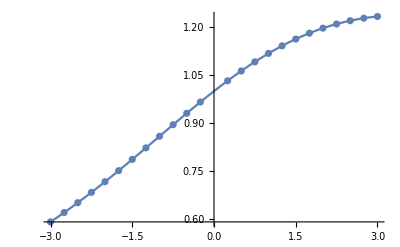

```mathematica
Show[{Plot[sStarFNet/.{t0->1,κ->κv},{κv,-3,3}],ListPlot[Table[{κv,s/.((FindMinimum[(WStar8ChainRod2[1,1,1,s]-1*s)/.{N0->1,kT->1,κ->κv,n->1,κ2->0},{s,1}])[[2]])},{κv,-3,3,0.25}]]}]
```

### Full DE chain energy

```mathematica
fe[λ_,κ_,κperp_]:=If[κ≠0,Re[λ*κ/(LangInv[λ])-κperp+(1-λ^2)*(-κ/3+Log[(2*Sqrt[κ])/(Sqrt[π]*Erf[Sqrt[κ]])])],0];
fo[λ_,rhat_,κ_]:=κ*(1-3*λ/(LangInv[λ]))*(rhat[[3]])^2
feap[r_,n_,b_,κ_,κperp_]:=Module[{λ,rhat},
λ=Norm[r]/(n*b);
rhat=If[Norm[r]>0,r/Norm[r],{0,0,0}];
Return[WLang[λ]+fe[λ,κ,κperp]+fo[λ,rhat,κ]]
];
```

```mathematica
Clear[DEFullChain]
```

```mathematica
DE8Chain[Fv_,κ_,κperp_,ω_,nv_:100,bv_:1]:=Module[{rs},
rs=Table[N[Fv.QRod[ω].(c8Rs[[i]]/.{r0->bv*√nv})],{i,1,8}];
Return[nv*Sum[feap[rs[[i]],nv,bv,κ,κperp],{i,1,8}]/8];
]
DE8ChainOldShear[sv_,κ_,κperp_,nv_:100,bv_:1]:=Module[{rs},
rs=Table[N[((VShear.QShear.(c8Rs[[i]]/.{r0->bv*√nv}))/.{s->sv})],{i,1,8}];
Return[nv*Sum[feap[rs[[i]],nv,bv,κ,κperp],{i,1,8}]/8];
]
DE3Chain[Fv_,κ_,κperp_,ω_,nv_:100,bv_:1]:=Module[{rs},
rs=Table[N[Fv.QRod[ω].(c3Rs[[i]]/.{r0->bv*√nv})],{i,1,3}];
Return[nv*Sum[feap[rs[[i]],nv,bv,κ,κperp],{i,1,3}]/3];
]
DE4Chain[Fv_,κ_,κperp_,ω_,nv_:100,bv_:1]:=Module[{rs},
rs=Table[N[Fv.QRod[ω].(c4Rs[[i]]/.{r0->bv*√nv})],{i,1,4}];
Return[nv*Sum[feap[rs[[i]],nv,bv,κ,κperp],{i,1,4}]/4];
]
DEFullChain[Fv_,κ_,κperp_,nv_:100,bv_:1]:=Module[{},
Return[
nv/(4*Pi)*NIntegrate[feap[(Fv.(bv*Sqrt[nv]*nHat[θv,ϕv])),nv,bv,κ,κperp]*Sin[θv],{ϕv,0,2*π},{θv,0,π}][[1]]
];
]
```

```mathematica
DE8Chain[FShear/.{s->1.0},0.0,0.0,{0.0,0.0,0.0}]
DE3Chain[FShear/.{s->1.0},0.0,0.0,{0.0,0.0,0.0}]
DEFullChain[(FShear/.{s->1.0}),0.0,0.0]
DE8ChainOldShear[1.0,0.0,0.0,100,1]
```

2.01012

2.0091

2.00971

2.00807

```mathematica
MinDE8Chain[F_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{DE8Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinDE3Chain[F_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{DE3Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinDE4Chain[F_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{DE4Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
```

```mathematica
FindMinDE8Chain[F_,κ_,κperp_,n_:100,b_:1,x0_:ω0]:=FindMinimum[{DE8Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]}}]
FindMinDE3Chain[F_,κ_,κperp_,n_:100,b_:1,x0_:ω0]:=FindMinimum[{DE3Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]}}]
FindMinDE4Chain[F_,κ_,κperp_,n_:100,b_:1,x0_:ω0]:=FindMinimum[{DE4Chain[F,κ,κperp,{ωx,ωy,ωz},n,b],{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]}}]
```

```mathematica
MinDE8ChainShear[t0_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{First[DE8Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz,sv}]
MinDE3ChainShear[t0_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{First[DE3Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz,sv}]
MinDE4ChainShear[t0_,κ_,κperp_,n_:100,b_:1]:=NMinimize[{First[DE4Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz,sv}]
MinDEFullShear[t0_,κ_,κperp_,n_:100,b_:1,x0:0.0]:=FindMinimum[DEFullChain[FShear/.{s->sv},κ,κperp,n,b]-t0*sv,{sv,x0}]
```

```mathematica
(*FindMinDE8ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE8Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
FindMinDE8ChainOldShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:0.0]:=FindMinimum[DE8ChainOldShear[sv,κ,κperp,n,b]-t0*sv,{sv,x0}]
FindMinDE3ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE3Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
FindMinDE4ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE4Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
FindMinDEFullShear[t0_,κ_,κperp_,n_:100,b_:1,x0:0.0]:=FindMinimum[DEFullChain[FShear/.{s->sv},κ,κperp,n,b]-t0*sv,{sv,x0}]*)
```

```mathematica
FindMinDE8ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[First[DE8Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}},Method->"ConjugateGradient"];
FindMinDE3ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[First[DE3Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}},Method->"ConjugateGradient"];
FindMinDE4ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[First[DE4Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}},Method->"ConjugateGradient"];
FindMinDEFullShear[t0_,κ_,κperp_,n_:100,b_:1,x0:0.0]:=FindMinimum[DEFullChain[FShear/.{s->sv},κ,κperp,n,b]-t0*sv,{sv,x0},Method->"ConjugateGradient"];
```

```mathematica
FindMinConsDE8ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE8Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
FindMinConsDE3ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE3Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
FindMinConsDE4ChainShear[t0_,κ_,κperp_,n_:100,b_:1,x0_:{ω0[[1]],ω0[[2]],ω0[[3]],0.0}]:=FindMinimum[{First[DE4Chain[FShear/.{s->sv},κ,κperp,{ωx,ωy,ωz},n,b]]-t0*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,x0[[1]]},{ωy,x0[[2]]},{ωz,x0[[3]]},{sv,x0[[4]]}}]
```

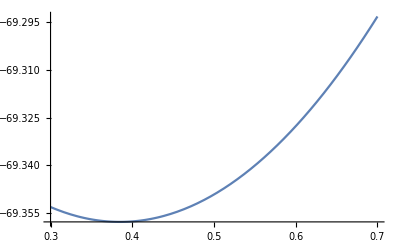

```mathematica
Plot[DE8ChainOldShear[sv,1.0,1.0,100,1]-0.5*sv,{sv,0.3,0.7}]
```

```mathematica
FindMinDE8ChainShear[0.5,1.0,1.0,100,1]
FindMinDE3ChainShear[0.5,1.0,1.0,100,1]
FindMinDE4ChainShear[0.5,1.0,1.0,100,1]
(*Quiet[MinDEFullShear[0.5,0.0001,0.0001,100,1,0.0]]*)
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,sv} = {-0.46304,0.494073,-0.765643,-16.2994}.

{-69.5991,{ωx→0.00517539,ωy→0.650145,ωz→0.0147154,sv→0.556331}}

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,sv} = {9.53259,-9.14212,-2.26422,-13.8139}.

{-521.032,{ωx→9.42742,ωy→-9.04201,ωz→-2.24091,sv→-13.8293}}

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,sv} = {7.59292,1.6971,-6.45572,-16.0728}.

{-69.5988,{ωx→0.453451,ωy→0.453451,ωz→0.453451,sv→0.555212}}

```mathematica
FindMinimum[{N[DE8Chain[(FShear/.{s->sv}),0.0001,0.0,{ωx,ωy,ωz}][[1]]]-0.5*sv,{ωx,ωy,ωz}∈Ball[]},{{ωx,Pi/(4*Sqrt[3])},{ωy,Pi/(4*Sqrt[3])},{ωz,Pi/(4*Sqrt[3])},{sv,0}}]
```

{1.38362,{ωx→1.71268×10^-6,ωy→0.663622,ωz→4.53869×10^-6,sv→0.496748}}

```mathematica
NMinimize[{N[DE8Chain[(FShear/.{s->sv}),0.0001,0.0,{ωx,ωy,ωz}][[1]]]-0.5*sv,{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz,sv}]
```

{1.38362,{ωx→0.0000131491,ωy→-0.907111,ωz→0.0000425057,sv→0.496747}}

```mathematica
(FShear/.{s->0.5})
```

{{1,0,0.5},{0,1,0},{0,0,1}}

```mathematica
DE3Chain[N[(FShear/.{s->0.5})],0.0,0.0,{0,0,0},25,1]
```

1.64699

```mathematica
FindMinimum[{N[DE3Chain[N[(FShear/.{s->0.25})],0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]
```

{1.5505,{ωx→0.199925,ωy→-0.0617888,ωz→-0.188235}}

Multiple initial guesses to check for multiple local minima

```mathematica
(*s0s={-0.5,2.0};
Do[
table={};
AppendTo[table,{"kappa","s31","s32","s41","s42","s81","s82","sFull1","sFull2","A31","A32","A41","A42","A81","A82","AFull1","AFull2"}];
Do[
κperp=If[κ>0,κ,0];
Chain3Solns=Table[FindMinDE3ChainShear[t0,κ,κperp,100,1,{ω0[[1]],ω0[[2]],ω0[[3]],s0}],{s0,s0s}];
Chain4Solns=Table[FindMinDE4ChainShear[t0,κ,κperp,100,1,{ω0[[1]],ω0[[2]],ω0[[3]],s0}],{s0,s0s}];
Chain8Solns=Table[FindMinDE8ChainShear[t0,κ,κperp,100,1,{ω0[[1]],ω0[[2]],ω0[[3]],s0}],{s0,s0s}];
(*ChainFullSolns=Quiet[Table[FindMinDEFullShear[t0,κ,κperp,100,1,s0],{s0,s0s}]];*)
AppendTo[table,{κ,sv/.Chain3Solns[[1]][[2]],sv/.Chain3Solns[[2]][[2]],sv/.Chain4Solns[[1]][[2]],sv/.Chain4Solns[[2]][[2]],sv/.Chain8Solns[[1]][[2]],sv/.Chain8Solns[[2]][[2]],
Chain3Solns[[1]][[1]],Chain3Solns[[2]][[1]],Chain4Solns[[1]][[1]],Chain4Solns[[2]][[1]],Chain8Solns[[1]][[1]],Chain8Solns[[2]][[1]]
}],
{κ,-3.0,3.0,0.1}];
Export["ShearMultipleSolns_t0-"<>ToString[Round[10*t0]]<>".csv",table],
{t0,{0.1,0.5,1.0,2.0}}
]*)
```

Parametric study

```mathematica
(*Do[
table={};
AppendTo[table,{"kappa","s3","s4","s8","sFull","A3","A4","A8","AFull","omega3x","omega3y","omega3z","omega4x","omega4y","omega4z","omega8x","omega8y","omega8z"}];
Chain3Soln=FindMinConsDE3ChainShear[t0,0,0,25,1];
Chain4Soln=FindMinConsDE4ChainShear[t0,0,0,25,1];
Chain8Soln=FindMinConsDE8ChainShear[t0,0,0,25,1];
x03={ωx,ωy,ωz,sv}/.Chain3Soln[[2]];
x04={ωx,ωy,ωz,sv}/.Chain4Soln[[2]];
x08={ωx,ωy,ωz,sv}/.Chain8Soln[[2]];
Do[
κperp=If[κ>0,κ,0];
Chain3Soln=FindMinDE3ChainShear[t0,κ,κperp,25,1,x03];
Chain4Soln=FindMinDE4ChainShear[t0,κ,κperp,25,1,x04];
Chain8Soln=FindMinDE8ChainShear[t0,κ,κperp,25,1,x08];
x03={ωx,ωy,ωz,sv}/.Chain3Soln[[2]];
x04={ωx,ωy,ωz,sv}/.Chain4Soln[[2]];
x08={ωx,ωy,ωz,sv}/.Chain8Soln[[2]];
(*ChainFullSoln=Quiet[MinDEFullShear[t0,κ,κperp,25,1,0.0]];*)
(*AppendTo[table,Catenate[{{κ,sv/.Chain3Soln[[2]],sv/.Chain4Soln[[2]],sv/.Chain8Soln[[2]],sv/.ChainFullSoln[[2]],
Re[Chain3Soln[[1]]],Re[Chain4Soln[[1]]],Re[Chain8Soln[[1]]],Re[ChainFullSoln[[1]]]},
{ωx,ωy,ωz}/.Chain3Soln[[2]],{ωx,ωy,ωz}/.Chain4Soln[[2]],{ωx,ωy,ωz}/.Chain8Soln[[2]]}]
],*)
AppendTo[table,Catenate[{{κ,sv/.Chain3Soln[[2]],sv/.Chain4Soln[[2]],sv/.Chain8Soln[[2]],0.0,
Re[Chain3Soln[[1]]],Re[Chain4Soln[[1]]],Re[Chain8Soln[[1]]],0.0},
{ωx,ωy,ωz}/.Chain3Soln[[2]],{ωx,ωy,ωz}/.Chain4Soln[[2]],{ωx,ωy,ωz}/.Chain8Soln[[2]]}]
],
{κ,-3.0,3.0,0.5}];
Export["Shear_n-25_t0-"<>ToString[Round[10*t0]]<>".csv",table],
{t0,{0.5,1.0,2.0}}
]*)
```

Visualize configurations

```mathematica
(*cF=5.0;
Do[
snapshots3Chain={};
snapshots4Chain={};
snapshots8Chain={};
table=Import["Shear_n-25_t0-"<>ToString[Round[10*t0]]<>".csv"];
For[i=2,i≤Length[table],i++,
Chain3Soln={table[[i]][[6]],{ωx->table[[i]][[10]],ωy->table[[i]][[11]],ωz->table[[i]][[12]],sv->table[[i]][[2]]}};
Chain4Soln={table[[i]][[7]],{ωx->table[[i]][[13]],ωy->table[[i]][[14]],ωz->table[[i]][[15]],sv->table[[i]][[3]]}};
Chain8Soln={table[[i]][[8]],{ωx->table[[i]][[16]],ωy->table[[i]][[17]],ωz->table[[i]][[18]],sv->table[[i]][[4]]}};
ω03={ωx,ωy,ωz}/.Chain3Soln[[2]];
Fv=(FShear/.{s->sv})/.Chain3Soln[[2]];
AppendTo[snapshots3Chain,Block[{rs,λs},
rs=Table[Fv.QRod[ω03].c3Rs[[i]],{i,1,3}];
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,3}];
Graphics3D[{{Opacity[0.25],Parallelepiped[{0,0,0},rs/.{n->1,b->1}]},Table[{RGBColor[λs[[i]]*cF,0,1-λs[[i]]*cF],Arrow[{{0,0,0},rs[[i]]/.{b->1,n->1}}]},{i,1,3}]},Boxed->False,ViewPoint->Front]
]];
ω04={ωx,ωy,ωz}/.Chain4Soln[[2]];
Fv=(FShear/.{s->sv})/.Chain4Soln[[2]];
AppendTo[snapshots4Chain,Block[{rs,λs},
rs=Table[Fv.QRod[ω04].c4Rs[[i]],{i,1,4}];
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,4}];
Graphics3D[{{Opacity[0.25],Tetrahedron[rs/.{n->1,b->1}]},Table[{RGBColor[λs[[i]]*cF,0,1-λs[[i]]*cF],Arrow[{{0,0,0},rs[[i]]/.{b->1,n->1}}]},{i,1,4}]},Boxed->False,ViewPoint->Front]
]];
ω08={ωx,ωy,ωz}/.Chain8Soln[[2]];
Fv=(FShear/.{s->sv})/.Chain8Soln[[2]];
AppendTo[snapshots8Chain,Block[{rs,λs,Edges,edges,centroid},
Edges={{2,0,0},{0,2,0},{0,0,2}};
edges=Table[Fv.QRod[ω08].Edges[[i]],{i,1,3}];
centroid=Sum[edges[[i]],{i,1,3}]/2;
rs=Table[Fv.QRod[ω08].Rvecs[[i]],{i,1,8}];
λs=Table[Norm[rs[[i]]]/(n*b)/.{n->100,b->1},{i,1,8}];
Graphics3D[{{Opacity[0.25],Parallelepiped[{0,0,0},edges]},Table[{RGBColor[λs[[i]]*cF,0,1-λs[[i]]*cF],Arrow[{centroid,centroid+rs[[i]]/.{b->1,n->3}}]},{i,1,8}]},Boxed->False,ViewPoint->Front]
]];
];
For[i=1,i≤Length[snapshots3Chain],i++,
Export["DEShear_snapshots/DEShear_t0-"<>ToString[Round[10*t0]]<>"_3Chain_"<>ToString[i]<>".pdf",snapshots3Chain[[i]]]
];
For[i=1,i≤Length[snapshots4Chain],i++,
Export["DEShear_snapshots/DEShear_t0-"<>ToString[Round[10*t0]]<>"_4Chain_"<>ToString[i]<>".pdf",snapshots4Chain[[i]]]
];
For[i=1,i≤Length[snapshots8Chain],i++,
Export["DEShear_snapshots/DEShear_t0-"<>ToString[Round[10*t0]]<>"_8Chain_"<>ToString[i]<>".pdf",snapshots8Chain[[i]]]
],
{t0,{0.5,1.0,2.0}}
]*)
```

```mathematica
(*cF=2.0;
Do[
Fv=N[(FShear/.{s->sv})];
Print[Fv];
(*Chain3Soln0=FindMinimum[{N[DE3Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}];
Chain4Soln0=FindMinimum[{N[DE4Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}];
Chain8Soln0=FindMinimum[{N[DE8Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}];*)
Chain3Soln0=NMinimize[{N[DE3Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}];
Chain4Soln0=NMinimize[{N[DE4Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}];
Chain8Soln0=NMinimize[{N[DE8Chain[Fv,0.0,0.0,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}];
ω03={ωx,ωy,ωz}/.Chain3Soln0[[2]];
r30s=Table[Fv.QRod[ω03].c3Rs[[i]],{i,1,3}]/.{n->25,b->1};
ω04={ωx,ωy,ωz}/.Chain4Soln0[[2]];
r40s=Table[Fv.QRod[ω04].c4Rs[[i]],{i,1,4}]/.{n->25,b->1};
ω08={ωx,ωy,ωz}/.Chain8Soln0[[2]];
r80s=Table[Fv.QRod[ω08].Rvecs[[i]],{i,1,8}]/.{n->25,b->1};
Print[{ω03,ω04,ω08}];
ω3=ω03;
ω4=ω04;
ω8=ω08;
table={};
AppendTo[table,{"kappa","frameDiff3","frameDiff4","frameDiff8","omega3x","omega3y","omega3z","omega4x","omega4y","omega4z","omega8x","omega8y","omega8z"}];
Do[
κperp=If[κ>0,κ,0];
(*Chain3Soln=FindMinimum[{N[DE3Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω03[[1]]},{ωy,ω03[[2]]},{ωz,ω03[[3]]}}];
Chain4Soln=FindMinimum[{N[DE4Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω04[[1]]},{ωy,ω04[[2]]},{ωz,ω04[[3]]}}];
Chain8Soln=FindMinimum[{N[DE8Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{ωx,ωy,ωz}∈Ball[]},{{ωx,ω08[[1]]},{ωy,ω08[[2]]},{ωz,ω08[[3]]}}];*)
Chain3Soln=FindMinimum[N[DE3Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{{ωx,ω03[[1]]},{ωy,ω03[[2]]},{ωz,ω03[[3]]}},Method->"ConjugateGradient"];
Chain4Soln=FindMinimum[N[DE4Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{{ωx,ω04[[1]]},{ωy,ω04[[2]]},{ωz,ω04[[3]]}},Method->"ConjugateGradient"];
Chain8Soln=FindMinimum[N[DE8Chain[Fv,κ,κperp,{ωx,ωy,ωz},25,1][[1]]],{{ωx,ω08[[1]]},{ωy,ω08[[2]]},{ωz,ω08[[3]]}},Method->"ConjugateGradient"];
ω3={ωx,ωy,ωz}/.Chain3Soln[[2]];
r3s=Table[Fv.QRod[ω3].c3Rs[[i]],{i,1,3}]/.{n->25,b->1};
λ3s=Table[(Norm[r3s[[i]]]/(n*b))/.{n->25,b->1},{i,1,3}];
(*d3=Sum[Norm[(r3s[[i]]-r30s[[i]])],{i,1,3}]/3;*)
d3=DiffFrame[r3s,r30s];
ω4={ωx,ωy,ωz}/.Chain4Soln[[2]];
r4s=Table[Fv.QRod[ω4].c4Rs[[i]],{i,1,4}]/.{n->25,b->1};
λ4s=Table[(Norm[r4s[[i]]]/(n*b))/.{n->25,b->1},{i,1,4}];
(*d4=Sum[Norm[(r4s[[i]]-r40s[[i]])],{i,1,4}]/4;*)
d4=DiffFrame[r4s,r40s];
ω8={ωx,ωy,ωz}/.Chain8Soln[[2]];
r8s=Table[Fv.QRod[ω8].Rvecs[[i]],{i,1,8}]/.{n->25,b->1};
λ8s=Table[(Norm[r8s[[i]]]/(n*b))/.{n->25,b->1},{i,1,8}];
(*d8=Sum[Norm[(r8s[[i]]-r80s[[i]])],{i,1,8}]/8;*)
d8=DiffFrame[r8s,r80s];
AppendTo[table,Catenate[{{κ,d3,d4,d8},{ωx,ωy,ωz}/.Chain3Soln[[2]],{ωx,ωy,ωz}/.Chain4Soln[[2]],{ωx,ωy,ωz}/.Chain8Soln[[2]]}]]
,
{κ,-5.0,5.0,0.5}];
Export["Shear_n-25_s-"<>ToString[Round[10*sv]]<>".csv",table],
{sv,{0.2,0.5,1.0,2.0,3.0}}
]*)
```

## Biomolecules

Example from Sun, Prashant, et. al. PRSA 2020

```mathematica
ω0={π/4,π/4,π/4}/Sqrt[3];
Norm[ω0]
```

π/4

```mathematica
QRod[{0,0,0}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
f4[λ_,d_]:=d.{(λ-1)^2/2,(λ-1)^3/3,(λ-1)^4/4}
```

```mathematica
d0={64,-16,0.8};
λStarBio={1,1-(d0[[2]]+Sqrt[d0[[2]]^2-4*d0[[1]]*d0[[3]]])/(2*d0[[3]]),1+(-d0[[2]]+Sqrt[d0[[2]]^2-4*d0[[1]]*d0[[3]]])/(2*d0[[3]])}
```

{1,6.52786,15.4721}

```mathematica
f4[0,d0]
```

37.5333

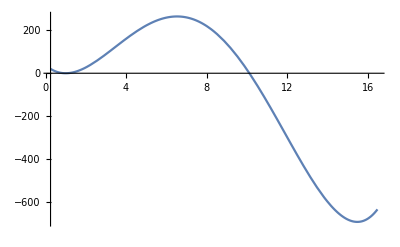

```mathematica
Plot[f4[λ,d0],{λ,0.25,λStarBio[[3]]+1}]
```

```mathematica
Bio8Chain[Fv_,d_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].c8Rs[[i]]/(r0)]],{i,1,8}];
Return[Sum[f4[λs[[i]],d],{i,1,8}]/8];
]
```

```mathematica
FTest1={{λ,0,0},{0,1,0},{0,0,1}}
```

{{λ,0,0},{0,1,0},{0,0,1}}

```mathematica
Simplify[Bio8Chain[FTest1/.{λ->0.8},d0,{0,0,0}],λ∈Reals]
```

0.123947

```mathematica
N[π/2]
```

1.5708

```mathematica
Simplify[Bio8Chain[FTest1/.{λ->0.8},d0,{0,0,0}]]
```

0.123947

```mathematica
Manipulate[
BioTestMinResult=FindMinimum[Bio8Chain[FTest1/.{λ->λv},d0,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[1]]},{ωz,ω0[[1]]}}];
{BioTestMinResult,Simplify[N[Bio8Chain[FTest1/.{λ->λv},d0,{0.0,0.0,0.0}]]],Plot[Bio8Chain[FTest1/.{λ->λv},d0,(ϵ*{ωx,ωy,ωz})/.BioTestMinResult[[2]]],{ϵ,ϵlb,ϵub}]},
{{λv,0.8},0.0,10.0,0.25},{{ϵlb,0.9},0.0,1.0,0.1},{{ϵub,1.1},1.0,5.0,0.1}]
```

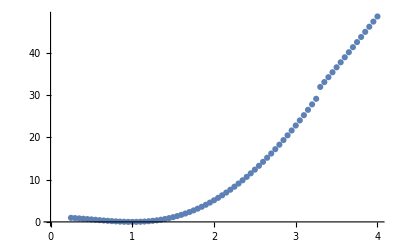

```mathematica
lp=Quiet[ListPlot[Table[{λv,FindMinimum[Bio8Chain[FTest1/.{λ->λv},d0,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[1]]},{ωz,ω0[[1]]}}][[1]]},{λv,0.25,4.0,0.05}]]]
```

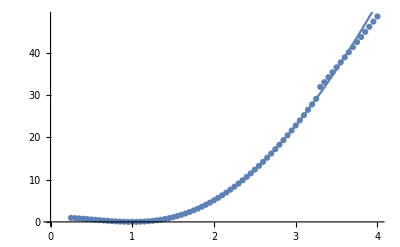

```mathematica
Show[{lp,Plot[Simplify[N[Bio8Chain[FTest1/.{λ->λv},d0,{0.0,0.0,0.0}]]],{λv,0.25,4.0}]}]
```

```mathematica
FTest2={{λ,0,0},{0,1/Sqrt[λ],0},{0,0,1/Sqrt[λ]}}
```

{{λ,0,0},{0,1/(√λ),0},{0,0,1/(√λ)}}

```mathematica
λlb=0.5;λub=2;
```

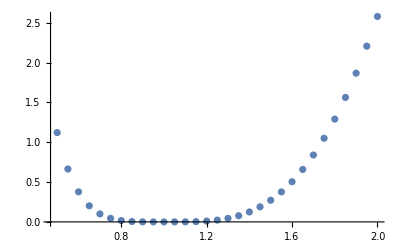

```mathematica
lp2=Quiet[ListPlot[Table[{λv,FindMinimum[Bio8Chain[FTest2/.{λ->λv},d0,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[1]]},{ωz,ω0[[1]]}}][[1]]},{λv,λlb,λub,0.05}]]]
```

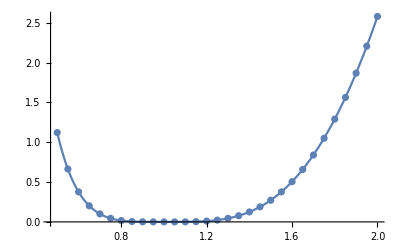

```mathematica
Show[{lp2,Plot[Simplify[N[Bio8Chain[FTest2/.{λ->λv},d0,{0.0,0.0,0.0}]]],{λv,λlb,λub}]}]
```

Example from Grekas et. al., Journal of the Royal Society Interface, 2021

```mathematica
STest=μ*(x^3-1);
wTest0=Integrate[STest,{x,1,λ}]
```

(3 μ)/4-λ μ+(λ^4 μ)/4

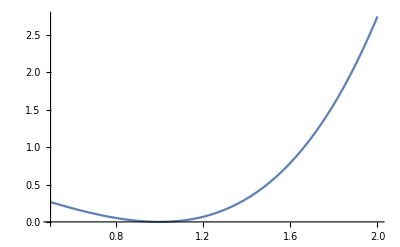

```mathematica
Plot[wTest0/.{μ->1},{λ,0.5,2}]
```

```mathematica
Bio8Chain2[Fv_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].c8Rs[[i]]/(r0)]],{i,1,8}];
Return[Sum[λs[[i]]^4/4-λs[[i]],{i,1,8}]/8];
]
```

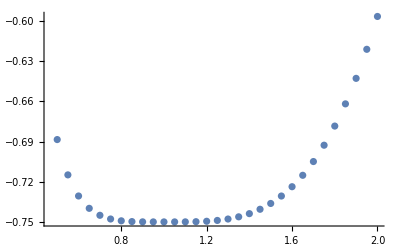

```mathematica
lp3=Quiet[ListPlot[Table[{λv,FindMinimum[Bio8Chain2[FTest2/.{λ->λv},{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[1]]},{ωz,ω0[[1]]}}][[1]]},{λv,λlb,λub,0.05}]]];
Show[{lp3,Plot[Simplify[N[Bio8Chain2[FTest2/.{λ->λv},d0,{0.0,0.0,0.0}]]],{λv,λlb,λub}]}]
```

My own cooking...

```mathematica
wTest1[λ_,ϵ0_]:=((λ-1+ϵ0)^2-ϵ0^2)^2/(ϵ0^4)
```

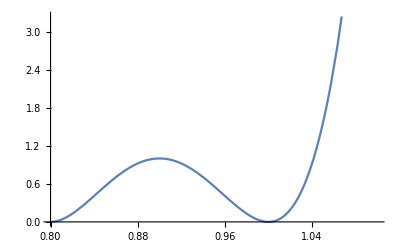

```mathematica
Plot[wTest1[λ,0.1],{λ,0.8,1.1}]
```

```mathematica
wTest2[λ_,ϵ0_]:=((λ-1)^2-ϵ0^2)^2*(λ-1)^2/(ϵ0^6)
```

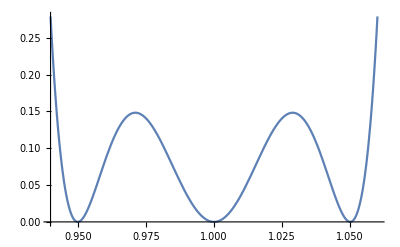

```mathematica
Plot[wTest2[λ,0.05],{λ,0.94,1.06}]
```

```mathematica
StretchStats8Chain[Fv_,ω_]:=Module[{λs,μλ,σλ,varλ},
λs=Simplify[Table[N[Norm[Fv.QRod[ω].c8Rs[[i]]/(r0)]],{i,1,8}]];
μλ=Simplify[Sum[λs[[i]],{i,1,8}]/8];
varλ=Simplify[Sum[(λs[[i]]-μλ)^2,{i,1,8}]/8];
σλ=Simplify[Sqrt[varλ]];
Return[{μλ,σλ,varλ,Min[λs],Max[λs],λs}];
]
```

```mathematica
Manipulate[StretchStats8Chain[FTest2/.{λ->λv},{ωx,ωy,ωz}],{{λv,0.8},0.0,10.0,0.25},{{ωx,ω0[[1]]},0.0,π/2,π/8},{{ωy,ω0[[1]]},0.0,π/2,π/8},{{ωz,ω0[[1]]},0.0,π/2,π/8}]
```

```mathematica
Clear[Bio8Chain3];
Clear[Bio3Chain];
Clear[Bio4Chain];
```

```mathematica
c6Rs=Catenate[{c3Rs,-c3Rs}]
```

{{r0,0,0},{0,r0,0},{0,0,r0},{-r0,0,0},{0,-r0,0},{0,0,-r0}}

```mathematica
Bio8Chain3[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c8Rs[[i]]/r0)]],{i,1,8}];
Return[Sum[wTest1[λs[[i]],ϵ0],{i,1,8}]/8];
]
Bio3Chain[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c3Rs[[i]]/r0)]],{i,1,3}];
Return[Sum[wTest1[λs[[i]],ϵ0],{i,1,3}]/3];
]
Bio4Chain[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c4Rs[[i]]/r0)]],{i,1,4}];
Return[Sum[wTest1[λs[[i]],ϵ0],{i,1,4}]/4];
]
Bio6Chain[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c6Rs[[i]]/r0)]],{i,1,6}];
Return[Sum[wTest1[λs[[i]],ϵ0],{i,1,6}]/6];
]
```

```mathematica
Bio3Chain[FTest2/.{λ->1.1},0.1,{π/4,π/4,π/4}]
Bio4Chain[FTest2/.{λ->1.1},0.1,{π/4,π/4,π/4}]
```

0.805697

0.610014

```mathematica
MinBio8Chain[F_,ϵ0_]:=NMinimize[{Bio8Chain3[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio3Chain[F_,ϵ0_]:=NMinimize[{Bio3Chain[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio4Chain[F_,ϵ0_]:=NMinimize[{Bio4Chain[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio6Chain[F_,ϵ0_]:=NMinimize[{Bio6Chain[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
```

```mathematica
MinBio8Chain[FTest2/.{λ->1.1},0.1]
MinBio3Chain[FTest2/.{λ->1.1},0.1]
MinBio4Chain[FTest2/.{λ->1.1},0.1]
```

{0.00919981,{ωx→0.0429641,ωy→-6.05923×10^-9,ωz→-9.07206×10^-9}}

{0.00919981,{ωx→0.212709,ωy→0.594565,ωz→0.750279}}

{0.00919981,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}

```mathematica
Map[Length,{9.199813740945531*^-7,{ωx->-0.1557536196170153,ωy->-0.6770494118036565,ωz->-0.3997314945615023}},{1}]
```

{0,3}

```mathematica
FTest3={{λ,0,0},{0,1,0},{0,0,1}}
```

{{λ,0,0},{0,1,0},{0,0,1}}

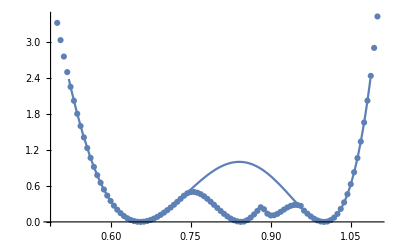

```mathematica
λlb=0.5;
λub=1.1;
lp4=Quiet[ListPlot[Table[{λv,FindMinimum[Bio8Chain3[FTest3/.{λ->λv},0.05,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[1]]},{ωz,ω0[[1]]}}][[1]]},{λv,λlb,λub,0.00625}]]];
Show[{lp4,Plot[Simplify[N[Bio8Chain3[FTest3/.{λ->λv},0.05,{0.0,0.0,0.0}]]],{λv,λlb,λub}]}]
```

```mathematica
dλ=0.00625;
λlb=0.5;λub=1.1;
ϵ0v=0.05;
(*Test3MinResults=Quiet[Table[{λv,FindMinimum[Bio8Chain3[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];
Test4ChainMinResults=Quiet[Table[{λv,FindMinimum[Bio3Chain[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];
Test3ChainMinResults=Quiet[Table[{λv,FindMinimum[Bio4Chain[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];*)
Test3MinResults=Quiet[Table[{λv,MinBio8Chain[FTest3/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test4ChainMinResults=Quiet[Table[{λv,MinBio4Chain[FTest3/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test3ChainMinResults=Quiet[Table[{λv,MinBio3Chain[FTest3/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test6ChainMinResults=Quiet[Table[{λv,MinBio6Chain[FTest3/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
```

This is a beautiful result!

```mathematica
Test3MinResults
```

{{0.5,{3.31492,{ωx→0.0429657,ωy→-8.07491×10^-9,ωz→-6.69305×10^-9}}},{0.50625,{3.02769,{ωx→0.0429657,ωy→-2.74976×10^-9,ωz→-5.73257×10^-9}}},{0.5125,{2.75447,{ωx→0.0429657,ωy→-6.37609×10^-9,ωz→-7.38173×10^-9}}},{0.51875,{2.49526,{ωx→0.0429657,ωy→-7.02064×10^-9,ωz→-7.41389×10^-9}}},{0.525,{2.25002,{ωx→0.0429657,ωy→-6.97632×10^-9,ωz→-6.96661×10^-9}}},{0.53125,{2.01868,{ωx→0.0429657,ωy→-7.45579×10^-9,ωz→-7.4886×10^-9}}},{0.5375,{1.80116,{ωx→0.0429657,ωy→-6.5554×10^-9,ωz→-6.93412×10^-9}}},{0.54375,{1.59735,{ωx→0.0429657,ωy→-9.04235×10^-11,ωz→-5.50465×10^-9}}},{0.55,{1.4071,{ωx→0.0429657,ωy→-7.07793×10^-9,ωz→-7.49747×10^-9}}},{0.55625,{1.23025,{ωx→0.0429657,ωy→-7.45624×10^-9,ωz→-7.57878×10^-9}}},{0.5625,{1.06662,{ωx→0.0429657,ωy→-7.02361×10^-9,ωz→-7.43892×10^-9}}},{0.56875,{0.915979,{ωx→0.0429657,ωy→-4.76649×10^-9,ωz→-7.75928×10^-9}}},{0.575,{0.778105,{ωx→0.0429657,ωy→-8.49607×10^-9,ωz→-7.33496×10^-9}}},{0.58125,{0.652734,{ωx→0.0429657,ωy→-7.02677×10^-9,ωz→-7.28812×10^-9}}},{0.5875,{0.539582,{ωx→0.0429656,ωy→-2.81112×10^-9,ωz→-8.37242×10^-9}}},{0.59375,{0.438347,{ωx→0.0429657,ωy→-7.71394×10^-9,ωz→-7.49736×10^-9}}},{0.6,{0.348701,{ωx→0.0429657,ωy→-5.9674×10^-9,ωz→-7.9661×10^-9}}},{0.60625,{0.270297,{ωx→0.0429657,ωy→-6.63068×10^-9,ωz→-7.09801×10^-9}}},{0.6125,{0.202771,{ωx→0.0429657,ωy→-7.66325×10^-9,ωz→-7.11774×10^-9}}},{0.61875,{0.145734,{ωx→0.0429657,ωy→-6.72312×10^-9,ωz→-7.19233×10^-9}}},{0.625,{0.098784,{ωx→0.0429657,ωy→-7.41813×10^-9,ωz→-7.2284×10^-9}}},{0.63125,{0.0614989,{ωx→0.0429657,ωy→-7.36362×10^-9,ωz→-7.63792×10^-9}}},{0.6375,{0.0334407,{ωx→0.0429657,ωy→-7.14344×10^-9,ωz→-7.46207×10^-9}}},{0.64375,{0.0141563,{ωx→0.0429657,ωy→-7.1169×10^-9,ωz→-7.23059×10^-9}}},{0.65,{0.00317772,{ωx→0.0429657,ωy→-7.38414×10^-9,ωz→-7.45448×10^-9}}},{0.65625,{0.0000241336,{ωx→0.0429657,ωy→-7.45515×10^-9,ωz→-7.4509×10^-9}}},{0.6625,{0.00420238,{ωx→0.0429657,ωy→-7.37662×10^-9,ωz→-7.37865×10^-9}}},{0.66875,{0.0152084,{ωx→0.0429657,ωy→-7.95664×10^-9,ωz→-7.38912×10^-9}}},{0.675,{0.0325286,{ωx→0.0429657,ωy→-5.3393×10^-9,ωz→-7.29617×10^-9}}},{0.68125,{0.0556407,{ωx→0.0429656,ωy→-7.66984×10^-9,ωz→-8.80861×10^-9}}},{0.6875,{0.0840157,{ωx→0.0429657,ωy→-9.08264×10^-9,ωz→-7.203×10^-9}}},{0.69375,{0.117119,{ωx→0.0429657,ωy→-8.62798×10^-9,ωz→-7.67855×10^-9}}},{0.7,{0.154411,{ωx→0.0429656,ωy→-7.60914×10^-9,ωz→-6.48115×10^-9}}},{0.70625,{0.195351,{ωx→0.0429656,ωy→-1.50229×10^-8,ωz→-9.22445×10^-10}}},{0.7125,{0.239396,{ωx→0.0429641,ωy→-1.28361×10^-8,ωz→-3.78665×10^-9}}},{0.71875,{0.286003,{ωx→0.0429641,ωy→-1.03242×10^-8,ωz→-1.01659×10^-8}}},{0.725,{0.334632,{ωx→0.0429641,ωy→-4.47205×10^-9,ωz→-7.50692×10^-9}}},{0.73125,{0.384746,{ωx→0.0429641,ωy→-1.54605×10^-8,ωz→-7.59139×10^-9}}},{0.7375,{0.435812,{ωx→0.032143,ωy→-0.000165994,ωz→0.0103219}}},{0.74375,{0.47609,{ωx→-0.078756,ωy→0.00383529,ωz→0.0972698}}},{0.75,{0.49637,{ωx→-0.101204,ωy→0.00709778,ωz→0.139918}}},{0.75625,{0.499124,{ωx→-0.0304136,ωy→0.00266764,ωz→0.174963}}},{0.7625,{0.486829,{ωx→-0.0449659,ωy→0.00465686,ωz→0.206358}}},{0.76875,{0.461954,{ωx→-0.0368286,ωy→0.00436557,ωz→0.235947}}},{0.775,{0.426945,{ωx→-0.0366712,ωy→0.00488064,ωz→0.264599}}},{0.78125,{0.384211,{ωx→-0.0366193,ωy→0.00540257,ωz→0.292921}}},{0.7875,{0.33611,{ωx→-0.0373412,ωy→0.00605295,ωz→0.321364}}},{0.79375,{0.284931,{ωx→0.530246,ωy→-0.341912,ωz→-0.0938527}}},{0.8,{0.232874,{ωx→0.198342,ωy→-0.37896,ωz→-0.0381701}}},{0.80625,{0.182033,{ωx→-0.0370831,ωy→0.00773868,ωz→0.411415}}},{0.8125,{0.134374,{ωx→-0.0370712,ωy→0.00837877,ωz→0.444515}}},{0.81875,{0.0917093,{ωx→-0.0378749,ωy→0.00927458,ωz→0.480238}}},{0.825,{0.0556751,{ωx→-0.0375165,ωy→0.00997625,ωz→0.51974}}},{0.83125,{0.0277026,{ωx→-0.0331101,ωy→0.00961352,ωz→0.565106}}},{0.8375,{0.00898944,{ωx→-0.0350681,ωy→0.0112551,ωz→0.621059}}},{0.84375,{0.000467036,{ωx→-0.24867,ωy→-0.703789,ωz→0.0918774}}},{0.85,{0.00581724,{ωx→-0.23902,ωy→-0.781145,ωz→0.0990055}}},{0.85625,{0.0312824,{ωx→-0.285655,ωy→-0.779321,ωz→0.118322}}},{0.8625,{0.0723572,{ωx→-0.310476,ωy→-0.778217,ωz→0.128603}}},{0.86875,{0.124301,{ωx→-0.127799,ωy→-0.784183,ωz→0.052936}}},{0.875,{0.182756,{ωx→0.0736365,ωy→0.0305012,ωz→-0.784995}}},{0.88125,{0.243764,{ωx→0.0695464,ωy→0.028807,ωz→-0.785039}}},{0.8875,{0.21037,{ωx→0.21019,ωy→0.59556,ωz→0.74943}}},{0.89375,{0.137108,{ωx→0.208551,ωy→0.596207,ωz→0.748877}}},{0.9,{0.107975,{ωx→0.205148,ωy→0.597549,ωz→0.747728}}},{0.90625,{0.110556,{ωx→0.194774,ωy→0.601629,ωz→0.744214}}},{0.9125,{0.133901,{ωx→0.196592,ωy→0.600916,ωz→0.744831}}},{0.91875,{0.168528,{ωx→0.196592,ωy→0.600916,ωz→0.744831}}},{0.925,{0.206421,{ωx→0.198038,ωy→0.600347,ωz→0.745321}}},{0.93125,{0.24103,{ωx→0.142356,ωy→0.622022,ωz→0.726234}}},{0.9375,{0.267272,{ωx→0.115348,ωy→0.632383,ωz→0.716824}}},{0.94375,{0.281532,{ωx→-0.108922,ωy→-0.634833,ωz→0.71457}}},{0.95,{0.281659,{ωx→0.0162135,ωy→-0.681427,ωz→0.669558}}},{0.95625,{0.242193,{ωx→0.0395942,ωy→1.55795×10^-8,ωz→-5.85113×10^-8}}},{0.9625,{0.187267,{ωx→0.0395945,ωy→-2.69137×10^-8,ωz→-4.94655×10^-8}}},{0.96875,{0.136742,{ωx→0.0395941,ωy→-6.46786×10^-9,ωz→-9.12931×10^-9}}},{0.975,{0.091942,{ωx→0.0395947,ωy→3.5667×10^-8,ωz→-6.25418×10^-8}}},{0.98125,{0.0542884,{ωx→0.0429633,ωy→-8.69658×10^-9,ωz→-1.28019×10^-8}}},{0.9875,{0.0253074,{ωx→0.042964,ωy→-4.62789×10^-8,ωz→-1.37984×10^-7}}},{0.99375,{0.00663092,{ωx→0.0429651,ωy→2.11306×10^-7,ωz→-2.1629×10^-7}}},{1.,{2.43751×10^-30,{ωx→0.00942348,ωy→0.160764,ωz→0.13945}}},{1.00625,{0.00726755,{ωx→0.0429645,ωy→-2.73194×10^-8,ωz→4.9319×10^-8}}},{1.0125,{0.0304016,{ωx→0.0429635,ωy→-1.86893×10^-7,ωz→-1.96794×10^-7}}},{1.01875,{0.071488,{ωx→0.0429641,ωy→6.1709×10^-8,ωz→-9.25243×10^-8}}},{1.025,{0.132734,{ωx→0.0429641,ωy→-8.08427×10^-8,ωz→-1.47882×10^-7}}},{1.03125,{0.216471,{ωx→0.042964,ωy→-5.84451×10^-9,ωz→5.05034×10^-8}}},{1.0375,{0.325157,{ωx→0.0429641,ωy→-9.35569×10^-9,ωz→-5.39516×10^-9}}},{1.04375,{0.46138,{ωx→0.0429639,ωy→3.09981×10^-9,ωz→-1.05146×10^-8}}},{1.05,{0.627862,{ωx→0.0429641,ωy→-2.02815×10^-8,ωz→-1.37724×10^-8}}},{1.05625,{0.827462,{ωx→0.0429642,ωy→-1.65144×10^-8,ωz→-1.00473×10^-8}}},{1.0625,{1.06318,{ωx→0.0429642,ωy→-2.00607×10^-9,ωz→-3.81763×10^-8}}},{1.06875,{1.33815,{ωx→0.0429641,ωy→-9.03304×10^-9,ωz→-1.3004×10^-8}}},{1.075,{1.65566,{ωx→0.0429641,ωy→-1.627×10^-8,ωz→-1.06961×10^-8}}},{1.08125,{2.01914,{ωx→0.0429642,ωy→1.24467×10^-9,ωz→-1.39685×10^-8}}},{1.0875,{2.43219,{ωx→0.0429641,ωy→-2.12359×10^-8,ωz→-1.16434×10^-8}}},{1.09375,{2.89853,{ωx→0.0429642,ωy→-1.03277×10^-8,ωz→6.20216×10^-9}}},{1.1,{3.42208,{ωx→0.0429641,ωy→-1.00558×10^-8,ωz→7.1384×10^-9}}}}

```mathematica
Test4ChainMinResults
```

{{0.5,{3.31492,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.50625,{3.02769,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.5125,{2.75447,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.51875,{2.49526,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.525,{2.25002,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.53125,{2.01868,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.5375,{1.80116,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.54375,{1.59735,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.55,{1.4071,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.55625,{1.23025,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.5625,{1.06662,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.56875,{0.915979,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.575,{0.778105,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.58125,{0.652734,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.5875,{0.539582,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.59375,{0.438347,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.6,{0.348701,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.60625,{0.270297,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.6125,{0.202771,{ωx→-0.157893,ωy→-0.67752,ωz→-0.398979}}},{0.61875,{0.145734,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.625,{0.098784,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.63125,{0.0614989,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.6375,{0.0334407,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.64375,{0.0141563,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.65,{0.00317772,{ωx→-0.157892,ωy→-0.67752,ωz→-0.398979}}},{0.65625,{0.0000241336,{ωx→-0.201344,ωy→-0.686962,ωz→-0.383613}}},{0.6625,{0.00420238,{ωx→-0.201344,ωy→-0.686962,ωz→-0.383613}}},{0.66875,{0.0152084,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.675,{0.0325286,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.68125,{0.0556407,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.6875,{0.0840157,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.69375,{0.117119,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.7,{0.154411,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.70625,{0.195351,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.7125,{0.239396,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.71875,{0.286003,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.725,{0.334632,{ωx→-0.195431,ωy→-0.685691,ωz→-0.385714}}},{0.73125,{0.384746,{ωx→-0.196382,ωy→-0.685896,ωz→-0.385376}}},{0.7375,{0.435812,{ωx→-0.190612,ωy→-0.675596,ωz→-0.382428}}},{0.74375,{0.47609,{ωx→-0.255725,ωy→-0.611334,ωz→-0.320063}}},{0.75,{0.49637,{ωx→0.200542,ωy→0.694825,ωz→0.613837}}},{0.75625,{0.499124,{ωx→0.0552122,ωy→0.504164,ωz→0.621995}}},{0.7625,{0.486829,{ωx→0.00649558,ωy→0.496968,ωz→0.635068}}},{0.76875,{0.461954,{ωx→-0.0175851,ωy→0.48331,ωz→0.653435}}},{0.775,{0.426945,{ωx→-0.0359841,ωy→0.468506,ωz→0.672586}}},{0.78125,{0.384211,{ωx→-0.0558247,ωy→0.454558,ωz→0.691184}}},{0.7875,{0.33611,{ωx→-0.460654,ωy→-0.43466,ωz→-0.174062}}},{0.79375,{0.284931,{ωx→-0.376862,ωy→-0.39891,ωz→-0.180062}}},{0.8,{0.232874,{ωx→-0.437581,ωy→-0.377223,ωz→-0.156661}}},{0.80625,{0.182033,{ωx→-0.705181,ωy→-0.369208,ωz→-0.0976838}}},{0.8125,{0.134374,{ωx→-0.722148,ωy→-0.337541,ωz→-0.0864778}}},{0.81875,{0.0917093,{ωx→-0.628297,ωy→-0.296477,ωz→-0.0913338}}},{0.825,{0.0556751,{ωx→-0.719078,ωy→-0.262752,ωz→-0.0681491}}},{0.83125,{0.0277026,{ωx→-0.658223,ωy→-0.215236,ωz→-0.0630616}}},{0.8375,{0.00898944,{ωx→-0.676467,ωy→-0.161095,ωz→-0.0457086}}},{0.84375,{0.000467036,{ωx→-0.678031,ωy→-0.0760696,ωz→-0.0215691}}},{0.85,{0.00581724,{ωx→-0.679229,ωy→-1.02889×10^-7,ωz→-3.21383×10^-8}}},{0.85625,{0.0312824,{ωx→-0.687852,ωy→-1.04385×10^-8,ωz→-7.68048×10^-9}}},{0.8625,{0.0723572,{ωx→-0.485916,ωy→-8.99695×10^-9,ωz→-9.8726×10^-9}}},{0.86875,{0.129361,{ωx→-0.0000393453,ωy→-0.952263,ωz→0.305278}}},{0.875,{0.186044,{ωx→5.048×10^-6,ωy→-0.944735,ωz→0.327835}}},{0.88125,{0.243764,{ωx→-0.29172,ωy→2.17611×10^-7,ωz→-4.78716×10^-7}}},{0.8875,{0.21037,{ωx→0.0846204,ωy→-0.377079,ωz→0.486685}}},{0.89375,{0.137108,{ωx→0.158501,ωy→-0.395676,ωz→0.472314}}},{0.9,{0.107975,{ωx→0.158501,ωy→-0.395676,ωz→0.472314}}},{0.90625,{0.110556,{ωx→0.106514,ωy→-0.382626,ωz→0.482478}}},{0.9125,{0.133901,{ωx→0.132983,ωy→-0.389292,ωz→0.477334}}},{0.91875,{0.168528,{ωx→0.132983,ωy→-0.389292,ωz→0.477334}}},{0.925,{0.206421,{ωx→0.108578,ωy→-0.383147,ωz→0.482079}}},{0.93125,{0.24103,{ωx→0.0506738,ωy→-0.368416,ωz→0.493122}}},{0.9375,{0.267272,{ωx→0.103398,ωy→-0.381838,ωz→0.483079}}},{0.94375,{0.281532,{ωx→0.00199435,ωy→-0.355865,ωz→0.502171}}},{0.95,{0.300295,{ωx→-0.157967,ωy→-0.677537,ωz→-0.398953}}},{0.95625,{0.242193,{ωx→-0.168886,ωy→-0.679931,ωz→-0.395107}}},{0.9625,{0.187267,{ωx→-0.157343,ωy→-0.677399,ωz→-0.399173}}},{0.96875,{0.136742,{ωx→-0.1582,ωy→-0.677588,ωz→-0.398871}}},{0.975,{0.091942,{ωx→-0.17074,ωy→-0.680336,ωz→-0.394453}}},{0.98125,{0.0542884,{ωx→-0.196258,ωy→-0.685869,ωz→-0.38542}}},{0.9875,{0.0253074,{ωx→-0.157983,ωy→-0.67754,ωz→-0.398948}}},{0.99375,{0.00663092,{ωx→-0.157983,ωy→-0.67754,ωz→-0.398948}}},{1.,{2.43751×10^-30,{ωx→0.20444,ωy→-0.597719,ωz→0.173236}}},{1.00625,{0.00726755,{ωx→-0.155754,ωy→-0.67705,ωz→-0.399731}}},{1.0125,{0.0304016,{ωx→-0.155752,ωy→-0.677049,ωz→-0.399732}}},{1.01875,{0.071488,{ωx→-0.155754,ωy→-0.677049,ωz→-0.399731}}},{1.025,{0.132734,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.03125,{0.216471,{ωx→-0.15726,ωy→-0.677381,ωz→-0.399202}}},{1.0375,{0.325157,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.04375,{0.46138,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.05,{0.627862,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.05625,{0.827462,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.0625,{1.06318,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.06875,{1.33815,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.075,{1.65566,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.08125,{2.01914,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.0875,{2.43219,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399202}}},{1.09375,{2.89853,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}},{1.1,{3.42208,{ωx→-0.157261,ωy→-0.677381,ωz→-0.399201}}}}

```mathematica
Export["Bio.csv",Block[{table,i,λi},
table={};
For[i=1,i≤Length[Test4ChainMinResults],i++,
λi=Test4ChainMinResults[[i]][[1]];
AppendTo[table,Catenate[{
{λi,Test3ChainMinResults[[i]][[2]][[1]],Test4ChainMinResults[[i]][[2]][[1]],Test3MinResults[[i]][[2]][[1]],Simplify[N[Bio8Chain3[FTest3/.{λ->λi},ϵ0v,{0.0,0.0,0.0}]]],Test6ChainMinResults[[i]][[2]][[1]]},
{ωx,ωy,ωz}/.Test3ChainMinResults[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test4ChainMinResults[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test3MinResults[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test6ChainMinResults[[i]][[2]][[2]]
}]
];
];
table
]]
```

Bio.csv

```mathematica
Bio8Chain4[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(Rvecs[[i]]/(b*Sqrt[n]))]],{i,1,8}];
Return[Sum[wTest2[λs[[i]],ϵ0],{i,1,8}]/8];
]
Bio3Chain4[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c3Rs[[i]]/(b*Sqrt[n]))]],{i,1,3}];
Return[Sum[wTest2[λs[[i]],ϵ0],{i,1,3}]/3];
]
Bio4Chain4[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c4Rs[[i]]/(b*Sqrt[n]))]],{i,1,4}];
Return[Sum[wTest2[λs[[i]],ϵ0],{i,1,4}]/4];
]
Bio6Chain4[Fv_,ϵ0_,ω_]:=Module[{λs},
λs=Table[N[Norm[Fv.QRod[ω].(c6Rs[[i]]/(b*Sqrt[n]))]],{i,1,6}];
Return[Sum[wTest2[λs[[i]],ϵ0],{i,1,6}]/6];
]
```

```mathematica
MinBio8Chain4[F_,ϵ0_]:=NMinimize[{Bio8Chain4[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio3Chain4[F_,ϵ0_]:=NMinimize[{Bio3Chain4[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio4Chain4[F_,ϵ0_]:=NMinimize[{Bio4Chain4[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
MinBio6Chain4[F_,ϵ0_]:=NMinimize[{Bio6Chain4[F,ϵ0,{ωx,ωy,ωz}],{ωx,ωy,ωz}∈Ball[]},{ωx,ωy,ωz}]
```

```mathematica
dλ=0.025;
λlb=0.5;λub=2;
ϵ0v=0.05;
(*Test3MinResults=Quiet[Table[{λv,FindMinimum[Bio8Chain3[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];
Test4ChainMinResults=Quiet[Table[{λv,FindMinimum[Bio3Chain[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];
Test3ChainMinResults=Quiet[Table[{λv,FindMinimum[Bio4Chain[FTest2/.{λ->λv},ϵ0v,{ωx,ωy,ωz}],{{ωx,ω0[[1]]},{ωy,ω0[[2]]},{ωz,ω0[[3]]}}]},{λv,λlb,λub,0.05}]];*)
Test8Chain4Results=Quiet[Table[{λv,MinBio8Chain4[FTest2/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test4Chain4MinResults=Quiet[Table[{λv,MinBio4Chain4[FTest2/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test3Chain4MinResults=Quiet[Table[{λv,MinBio3Chain4[FTest2/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
Test6Chain4MinResults=Quiet[Table[{λv,MinBio3Chain4[FTest2/.{λ->λv},ϵ0v]},{λv,λlb,λub,dλ}]];
```

NMinimize::nnum: The function value … is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.25 Power[«2»]+2. Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.275625 Power[«2»]+1.90476 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.3025 Power[«2»]+1.81818 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.25 Power[«2»]+2. Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.275625 Power[«2»]+1.90476 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.3025 Power[«2»]+1.81818 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

```mathematica
Test3Chain4MinResults
```

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.25 Power[«2»]+2. Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.275625 Power[«2»]+1.90476 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/3 (6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(0.3025 Power[«2»]+1.81818 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

{{0.5,NMinimize[{1/3 (6.4×10^7 (-0.0025+(-1+Norm[1])^2)^2 (-1+Norm[{{0.5,0.,0.},{0.,1.41421,0.},{0.,0.,1.41421}}.If[√(Abs[ωx]^2+Abs[ωy]^2+Abs[ωz]^2)>0.,Q[r$15137516,θ$15137516],IdentityMatrix[3.]].{r0/(b √n),0.,0.}])^2+6.4×10^7 (-0.0025+1)^2 (-1+Norm[1.1.{0.,r0/1,0.}])^2+6.4×10^7 (-0.0025+(-1+Norm[1])^2)^2 (-1+Norm[{{0.5,0.,0.},{0.,1.41421,0.},{0.,0.,1.41421}}.If[√1>0.,Q[r$15137518,θ$15137518],IdentityMatrix[3.]].{0.,0.,r0/(b √n)}])^2),{ωx,ωy,ωz}∈Ball[{0,0,0}]},{ωx,ωy,ωz}]},59,{2.,NMinimize[{1,1},1]}}
 |  |  |  |

```mathematica
Export["Bio3.csv",Block[{table,i,λi},
table={};
For[i=1,i≤Length[Test4Chain4MinResults],i++,
λi=Test4Chain4MinResults[[i]][[1]];
AppendTo[table,Catenate[{
{λi,Test3Chain4MinResults[[i]][[2]][[1]],Test4Chain4MinResults[[i]][[2]][[1]],Test8Chain4Results[[i]][[2]][[1]],Simplify[N[Bio8Chain4[FTest2/.{λ->λi},ϵ0v,{0.0,0.0,0.0}]]],Test6Chain4MinResults[[i]][[2]][[1]]},
{ωx,ωy,ωz}/.Test3Chain4MinResults[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test4Chain4MinResults[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test8Chain4Results[[i]][[2]][[2]],
{ωx,ωy,ωz}/.Test6Chain4MinResults[[i]][[2]][[2]]
}]
];
];
table
]]
```

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(2. Power[«2»]+0.25 Power[«2»]+2. Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(1.90476 Power[«2»]+0.275625 Power[«2»]+1.90476 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

NMinimize::nnum: The function value 1/4 (6.4×10^7 (-1+√(1.81818 Power[«2»]+0.3025 Power[«2»]+1.81818 Power[«2»]))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2+6.4×10^7 (-1+√(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2))^2 (-0.0025+(-1+√Plus[«3»])^2)^2) is not a number at {ωx,ωy,ωz} = {0.170467,-0.603355,-0.108689}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Part::partd: Part specification Rvecs⟦1⟧ is longer than depth of object.

Part::partd: Part specification Rvecs⟦2⟧ is longer than depth of object.

Part::partd: Part specification Rvecs⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {ωx,ωy,ωz} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Catenate::invrp: The argument {ωx,ωy,ωz}/.{ωx,ωy,ωz} is not a valid Association or a list.

General::stop: Further output of Catenate::invrp will be suppressed during this calculation.

Bio3.csv

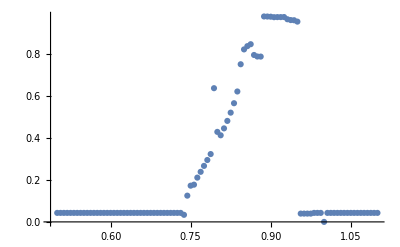

```mathematica
ListPlot[Table[{row[[1]],If[Abs[row[[2]][[1]]-Simplify[N[Bio8Chain3[FTest2/.{λ->row[[1]]},ϵ0v,{0.0,0.0,0.0}]]]]>10^-6,Mod[Norm[{ωx,ωy,ωz}/.row[[2]][[2]]],2*π],0]},{row,Test3MinResults}]]
```